```mathematica
双载流线圈在一些方向与位置上产生的磁场分布曲线
```

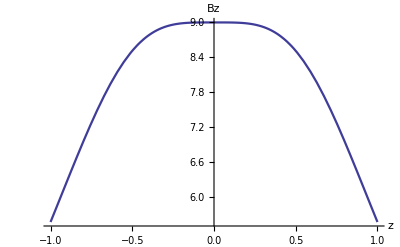

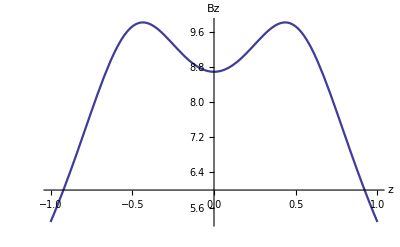

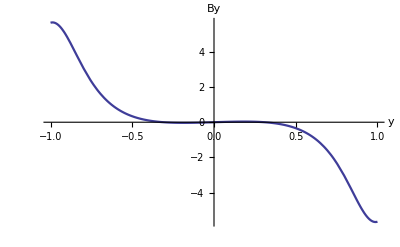

```mathematica
By0[y_,z_]:=
NIntegrate[(R*z*Sin[φ])/(z^2+y^2+R^2-2R*y*Sin[φ])^(3/2),
{φ,0,2π}];
Bz0[y_,z_]:=
NIntegrate[(R*(R-y*Sin[φ]))/((z^2+y^2+R^2-2R*y*Sin[φ])^(3/2)),
{φ,0,2π}];R=1.0;d=R;
By[y_,z_]:=By0[y,z-d/2]+By0[y,z+d/2];
Bz[y_,z_]:=Bz0[y,z-d/2]+Bz0[y,z+d/2];
Plot[Bz[0,z],{z,-d,d},AxesLabel->{"z","Bz"},
PlotRange->All,PlotStyle->Thickness[0.004],
AxesStyle->Thickness[0.003]]
Plot[Bz[R/2,z],{z,-d,d},AxesLabel->{"z","Bz"},
PlotRange->All,PlotStyle->Thickness[0.004],
AxesStyle->Thickness[0.003]]
Plot[By[y,d/4],{y,-R,R},AxesLabel->{"y","By"},
PlotRange->All,PlotStyle->Thickness[0.004],
AxesStyle->Thickness[0.003]]
Clear[d,R,By0,Bz0,By,Bz]
```